# CCBH and Power Law + Peak: Formation mass distribution for m2

Davi  C. Rodrigues (this code).  2023.

```mathematica
ResourceFunction["DarkMode"][]
```

CCBH = Cosmologically coupled Black Hole (arbitrary k value)
DEBH = Dark Energy coupled Black Hole (implies k = - 3w)
m1 = primary (larger) mass of the BBH or NSBH pair.

Naming conventions:
All defined variables/functions start with lower case letter.
“I" at the end of a function name: interpolated version. 
"Raw”: a function without options. It is useful to store results. The version with options is based on the raw version.

## Starting...

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Directories.wl";

(*
  Calling wl files
  ***************** 
*)
getCode["Constants.wl"];
baseSimPoints = 10^6; (*The base number of points to be simmulated for each dimension, commonly 10^5-10^7, depends on the purpose.*)

getCode["ObsDataPreparationGWTC-3.wl"]; (*Not essential for this notebook*)
getCode["PowerLawPlusPeakDefinition.wl"];
getCode["Cosmology.wl"];
getCode["MassFactorCorrection.wl"];

Print["End of running wl files."];

(*
  GENERAL PURPOSE FUNCTIONS
  **************************
*)

findSigma::usage = "findSigma[probability] yields the number of σ's for a given probability.";
findSigma[prob_] := Block[{sigma}, 
  sigma /. FindRoot[NProbability[Abs[x] > sigma , x\[Distributed]NormalDistribution[]] == prob, {sigma, 2}]
];

Clear[outSigma];
outSigma[n_] := outSigma[n] = NProbability[Abs[x] > n, x\[Distributed]NormalDistribution[]];
```

Starting Constants.wl:

Starting ObsDataPreparationGWTC-3.wl:

Number of m1 black holes:   72

Starting PowerLawPlusPeakDefinition.wl:

Use plpp`pi[m, options] for the power-law-plus-peak PDF and plpp`𝒟[options] for the distribution. Use optionsPlpp to see the options.

Starting Cosmology.wl:

tableZformation loaded.

Starting MassFactorCorrection.wl:

Base number of simmulated points per dimension (baseSimPoints):   1000000

"dataM1Merger"  7.42226

End of running wl files.

```mathematica
ParallelEvaluate[Off[NIntegrate::slwcon]];
plpp`listPiM2
```

{{1.,0.},{1.5,0.},{2.,0.},{2.5,0.},{3.,0.},{3.5,0.},{4.,0.},{4.5,0.},{5.,4.58453×10^-12},{5.5,0.00622028},{6.,0.0820044},{6.5,0.177129},{7.,0.223021},{7.5,0.227107},{8.,0.209451},{8.5,0.181323},{9.,0.14774},{9.5,0.113922},{10.,0.0873957},{10.5,0.0686684},{11.,0.053642},{11.5,0.0438876},{12.,0.0364799},{12.5,0.0307344},{13.,0.0262072},{13.5,0.0225799},{14.,0.0196474},{14.5,0.0172387},{15.,0.0152543},{15.5,0.0135998},{16.,0.0122065},{16.5,0.0110353},{17.,0.0100364},{17.5,0.00918394},{18.,0.00845334},{18.5,0.00782278},{19.,0.00727675},{19.5,0.00680321},{20.,0.00639084},{20.5,0.00603034},{21.,0.00571574},{21.5,0.00543837},{22.,0.00519632},{22.5,0.0049824},{23.,0.00479414},{23.5,0.00462819},{24.,0.00448198},{24.5,0.00435265},{25.,0.00423863},{25.5,0.00413781},{26.,0.00404977},{26.5,0.00397281},{27.,0.00390453},{27.5,0.00384493},{28.,0.00379281},{28.5,0.00374595},{29.,0.00370321},{29.5,0.00366222},{30.,0.00361814},{30.5,0.00356571},{31.,0.00349478},{31.5,0.00339726},{32.,0.00326056},{32.5,0.00307843},{33.,0.00284603},{33.5,0.0025668},{34.,0.00225279},{34.5,0.00192204},{35.,0.00159634},{35.5,0.00129659},{36.,0.00103787},{36.5,0.000828834},{37.,0.000669136},{37.5,0.000553427},{38.,0.000472896},{38.5,0.000417712},{39.,0.000379735},{39.5,0.000352312},{40.,0.000331352},{40.5,0.000313961},{41.,0.000298716},{41.5,0.000284811},{42.,0.000271889},{42.5,0.000259666},{43.,0.000248168},{43.5,0.000237322},{44.,0.000226951},{44.5,0.0002172},{45.,0.000207832},{45.5,0.000198978},{46.,0.000190572},{46.5,0.000182545},{47.,0.00017493},{47.5,0.000167633},{48.,0.000160715},{48.5,0.000154125},{49.,0.000147799},{49.5,0.000141772},{50.,0.000136021},{50.5,0.000130515},{51.,0.000125256},{51.5,0.000120232},{52.,0.000115425},{52.5,0.000110822},{53.,0.000106393},{53.5,0.000102151},{54.,0.0000980971},{54.5,0.0000941952},{55.,0.0000904289},{55.5,0.0000868713},{56.,0.0000834171},{56.5,0.0000801018},{57.,0.0000768982},{57.5,0.0000738322},{58.,0.0000708874},{58.5,0.000068049},{59.,0.0000652912},{59.5,0.0000626698},{60.,0.0000601344},{60.5,0.0000576767},{61.,0.0000553042},{61.5,0.000053051},{62.,0.000050835},{62.5,0.0000487129},{63.,0.0000466615},{63.5,0.0000446708},{64.,0.0000427576},{64.5,0.0000409087},{65.,0.0000391129},{65.5,0.000037387},{66.,0.000035706},{66.5,0.0000342102},{67.,0.0000325124},{67.5,0.000030976},{68.,0.0000295072},{68.5,0.0000280773},{69.,0.0000266893},{69.5,0.0000253446},{70.,0.0000240363},{70.5,0.0000227703},{71.,0.0000215405},{71.5,0.0000203438},{72.,0.0000191827},{72.5,0.000018056},{73.,0.0000169423},{73.5,0.0000158931},{74.,0.0000148586},{74.5,0.0000138494},{75.,0.0000128689},{75.5,0.0000119149},{76.,0.000010983},{76.5,0.0000100786},{77.,9.19773×10^-6},{77.5,8.32104×10^-6},{78.,7.50151×10^-6},{78.5,6.68523×10^-6},{79.,5.88852×10^-6},{79.5,5.11333×10^-6},{80.,4.35642×10^-6},{80.5,3.61697×10^-6},{81.,2.89534×10^-6},{81.5,2.19195×10^-6},{82.,1.50419×10^-6},{82.5,8.32496×10^-7},{83.,1.8071×10^-7},{83.5,0.},{84.,0.},{84.5,0.},{85.,0.},{85.5,0.},{86.,0.},{86.5,0.},{87.,0.},{87.5,0.},{88.,0.},{88.5,0.},{89.,0.},{89.5,0.},{90.,0.},{90.5,0.},{91.,0.},{91.5,0.},{92.,0.},{92.5,0.},{93.,0.},{93.5,0.},{94.,0.},{94.5,0.},{95.,0.},{95.5,0.},{96.,0.},{96.5,0.},{97.,0.},{97.5,0.},{98.,0.},{98.5,0.},{99.,0.},{99.5,0.},{100.,0.}}

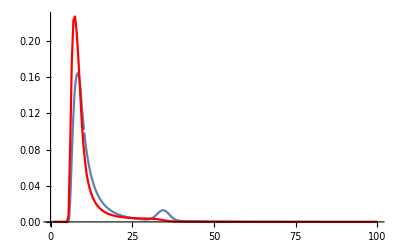

```mathematica
Show[Plot[plpp`pi[m1], {m1,0,100}, PlotPoints->40, PlotRange->All], ListPlot[plpp`listPiM2, Joined->True, PlotRange->All, PlotStyle->Red]]
```

```mathematica
plpp`piM2InormFactor
```

0.993952

```mathematica
plpp`piM2Inorm[m2_] :=  plpp`piM2InormFactor plpp`piM2I[m2]
```

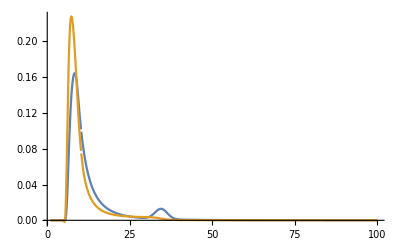

```mathematica
Plot[{plpp`pi[m1], plpp`piM2Inorm[m1]}, {m1,1,100}, PlotPoints->40, PlotRange->All]
```

```mathematica
#[RandomVariate[plpp`dist2[], 10^4]]  & /@  {Median, Mean} 
#[RandomVariate[plpp`dist[], 10^4]]  & /@  {Median, Mean}
```

{8.4992,10.4173}

{10.3072,13.705}

## Formation mass distribution

```mathematica
ClearAll[
  𝒟M1Formation, 
  𝒟M1FormationRaw
];

Clear[dataM2FormationRaw, dataM2Formation];
𝒟plp2 = plpp`𝒟2[]; 
dataM2Merger = RandomVariate[𝒟plp2, 2 baseSimPoints] ~ EchoTiming ~ "dataM2Merger"; 

dataM2FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_]:= dataM2FormationRaw[zObs, tdmin, tdmax, k, zMax, w]= Block[
  {length, dataM2MergerSameLength},
  length = Length @ dataMassFactor[zObs, tdmin, tdmax, k, zMax, w];
  dataM2MergerSameLength = Take[dataM2Merger, length];
  1/dataMassFactor[zObs, tdmin, tdmax, 1, zMax, w]^k dataM2MergerSameLength 
];

dataM2Formation[zObs_, opts:OptionsPattern[optionstkw]] := dataM2FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
]


𝒟M1FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M1FormationRaw[zObs, tdmin, tdmax, k, zMax, w] = SmoothKernelDistribution[
  dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w],
  0.05, 
  InterpolationPoints -> 10^5, 
  MaxExtraBandwidths -> {2,2}, (*This slightly extends the profile beyond data (about 0.1 solar mass). 
  It is only used for the plot. Use {0,0} for no extension.*)
  PerformanceGoal->"Quality"
];

𝒟M1Formation[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];
```

"dataM2Merger"  16.4461

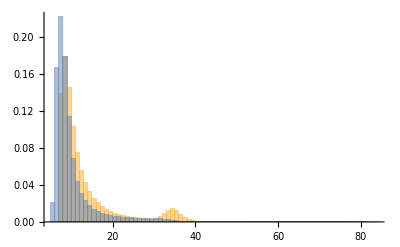

```mathematica
Histogram[{dataM1Merger, dataM2Merger}, {1}, "PDF", PlotRange->All]
```

```mathematica
Clear[𝒟M2FormationEmpRaw, 𝒟M2FormationEmp]
𝒟M2FormationEmpRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M2FormationEmpRaw[zObs, tdmin, tdmax, k, zMax, w] = 
 EmpiricalDistribution[
   dataM2FormationRaw[zObs, tdmin, tdmax, k, zMax, w]
 ];

𝒟M2FormationEmp[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M2FormationEmpRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

probabilityMminApprox2[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M2FormationEmp[0.4, opts], mMin]^71; (*Assumes 71 m2 BH masses.*)
probabilityMminDoubleApprox2[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M2FormationEmp[0.4, opts], mMin]^(2*71);
```

```mathematica
findSigma@probabilityMminApprox2[2]
```

4.01285

```mathematica
findSigma@probabilityMminDoubleApprox2[2]
```

5.94729

```mathematica
findSigma@probabilityMminApprox2[2.0]
```

4.07791

```mathematica
dataM2FormationRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_]
```

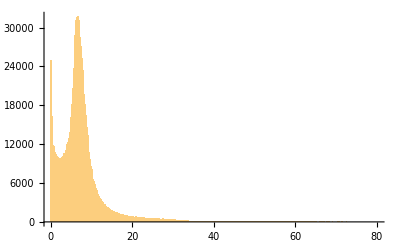

```mathematica
Histogram[dataM2FormationRaw[0.4, tdmin0, tdmax0, k0, zMax0, w0], {0.2}, PlotRange->All]
```

GENERATE SIMILAR PLOT THAT WAS USED FOR M1?

For each m1  I will find 10^3 m2. I need a p(m2|m1), normalized in m2 for each m1.

```mathematica
dataM2test[20]
```

$Aborted

```mathematica
dataM1Merger // Mean
dataM2Merger // Mean
```

13.5993

17.0308

```mathematica
NIntegrate[plpp`piM2[m2], {m2, 0,100}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m2 near {m2} = {25.7797}. NIntegrate obtained 1.00007 and 5.42656×10^-6 for the integral and error estimates.

1.00007

```mathematica
Clear[𝒟M2FormationEmpRaw, 𝒟M2FormationEmp]
𝒟M2FormationEmpRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M2FormationEmpRaw[zObs, tdmin, tdmax, k, zMax, w] = 
 EmpiricalDistribution[
   dataM2FormationRaw[zObs, tdmin, tdmax, k, zMax, w]
 ];

𝒟M2FormationEmp[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M2FormationEmpRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

probabilityMminApprox2[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M2FormationEmp[0.4, opts], mMin]^72;
probabilityMminDoubleApprox2[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M2FormationEmp[0.4, opts], mMin]^(2*72);
```

```mathematica
probabilityMminApprox2[2] // findSigma
```

3.3895

```mathematica
Plot[plpp`piM2I[x], {x, 1, 100}]
```

$Aborted

```mathematica
plpp`piM2Unnorm[1]
```

166.979

### Plots (Use ~10^7 data points)

This first plot probably will not get into the paper.

```mathematica
(*dataM1Formation[0.4]; //EchoTiming
dataM1Formation[0.4, k-> 0.5]; //EchoTiming
histFormation3 = Histogram[
  {dataM1Formation[0.4], dataM1Formation[0.4, k-> 0.5], dataM1Merger}, 
  {.2}, 
  "PDF", 
  PlotRange->{{0,50}, All},
  Background->White,
  ChartStyle->{Lighter@Orange, ColorData["AvocadoColors"][0.5], Lighter@Blue},
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  ChartLegends -> Placed[{
    Style["k = 3.0", FontFamily->"Times", FontSize -> 15], 
    Style["k = 0.5", FontFamily->"Times", FontSize -> 15], 
    Style["k = 0.0", FontFamily->"Times", FontSize -> 15]}, 
    {0.8, 0.75}
  ]
]

(*exportOut["histFormation3.pdf", histFormation3]*)*)
```

212.041

106.834

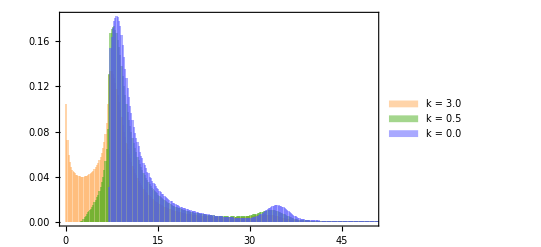

pathOut/histFormation3.pdf

```mathematica
tdmaxE = 5;
tdminE = 0.005;
zMaxE = 2;
𝒟M1Formation[0.4]; //EchoTiming
𝒟M1Formation[0.4, k-> 0.5]; //EchoTiming
𝒟M1Formation[0.4, tdmax -> tdmaxE]; //EchoTiming
𝒟M1Formation[0.4, tdmin -> tdminE]; //EchoTiming
𝒟M1Formation[0.4, zMax -> zMaxE]; //EchoTiming

legend1 = LineLegend[
  {Lighter@Orange, ColorData["AvocadoColors"][0.5], Lighter@Blue}, 
  {
    Style["k=3.0", FontFamily->"Times", FontSize -> 11], 
    Style["k=0.5", FontFamily->"Times", FontSize -> 11], 
    Style["k=0.0", FontFamily->"Times", FontSize -> 11]
  }, 
  LegendMarkerSize -> 20, 
  Spacings -> 0.15 (*It works, although in red*)
];

legend2 = LineLegend[
  {Directive[Lighter@Orange, Dashed], Directive[Lighter@Orange, Dotted], Directive[Lighter@Orange, DotDashed]}, 
  {
    Style["t_max=" <> ToString[Round@tdmaxE]<>" Gyr", FontFamily->"Times", FontSize -> 11], 
    Style["t_min=" <> ToString[Round[10^3 tdminE]]<>" Myr", FontFamily->"Times", FontSize -> 11],
    Style["z_max=" <> ToString[Round[zMaxE]], FontFamily->"Times", FontSize -> 11]
  }, 
  LegendMarkerSize -> 20, 
  Spacings -> 0.15 (*It works, although in red*)
];

tickLarge = 0.015;
tickSmall = 0.006;
frameTicksSmall = Flatten[Table[{n 10^i, "", tickSmall}, {n,1,10}, {i, -4, 0, 1}],1];
frameTicksLarge = Table[{10^i, Superscript[10, i], tickLarge}, {i, -4, 0, 1}];
frameTicksLargeDumb = Table[{10^i, "", tickLarge}, {i, -4, 0, 1}];
frameTicks = Flatten[Join[{frameTicksSmall, frameTicksLarge}],1];
frameTicksDumb = Flatten[Join[{frameTicksSmall, frameTicksLargeDumb}],1];


Off[General::munfl]; 
plotPDFformationDist = LogLogPlot[
  {
    PDF[𝒟M1Formation[0.4], x], 
    PDF[𝒟M1Formation[0.4, tdmax -> tdmaxE], x], 
    PDF[𝒟M1Formation[0.4, tdmin -> tdminE], x], 
    PDF[𝒟M1Formation[0.4, zMax -> zMaxE], x],
    PDF[𝒟M1Formation[0.4, k-> 0.5], x], 
    PDF[𝒟plp, x]
  }, 
  {x, 0.5, plpp`mMax /. optionsPlpp}, 
  PlotRange->{{0.5, 500}, {8 10^-5, .3}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks->{{frameTicks, frameTicksDumb}, {Automatic, Automatic}},
  PlotPoints->5000,
  MaxRecursion->3,
  PlotStyle->{
    {Lighter@Orange}, 
    {Lighter@Orange, Dashed}, 
    {Lighter@Orange, Dotted}, 
    {Lighter@Orange, DotDashed}, 
    {ColorData["AvocadoColors"][0.5]}, 
    {Lighter@Blue}},
  PlotLegends-> {Placed[legend1, {0.60,0.81}], Placed[legend2, {0.85,0.81}]}
]
On[General::munfl];

exportOut["plotPDFformationDist.pdf", plotPDFformationDist]
```

2.15296

2.05971

0.983042

2.13426

2.02869

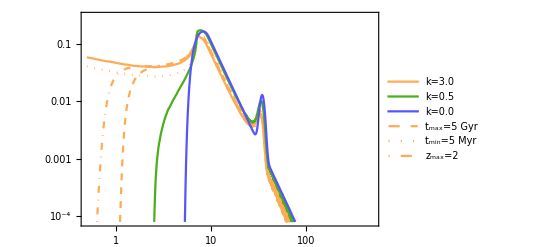

pathOut/plotPDFformationDist.pdf

## Probabilities for 2<m_th<5 (uses 10^7 Points) (EmpiricalCDF based, more precise and does not depend on bandwidth selection)

m_th is the threshold mass.

### Computing the relevant distributions

```mathematica
𝒟M1FormationEmpRaw[zObs_, tdmin_, tdmax_, k_, zMax_, w_] := 𝒟M1FormationEmpRaw[zObs, tdmin, tdmax, k, zMax, w] = 
 EmpiricalDistribution[
   dataM1FormationRaw[zObs, tdmin, tdmax, k, zMax, w]
 ];

𝒟M1FormationEmp[zObs_, opts:OptionsPattern[optionstkw]] := 𝒟M1FormationEmpRaw[
  zObs, 
  OptionValue @ tdmin, 
  OptionValue @ tdmax, 
  OptionValue @ k, 
  OptionValue @ zMax, 
  OptionValue @ w
];

probabilityMminApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^72;
probabilityMminDoubleApprox[mMin_, opts:OptionsPattern[optionstkw]] := SurvivalFunction[𝒟M1FormationEmp[0.4, opts], mMin]^(2*72);
```

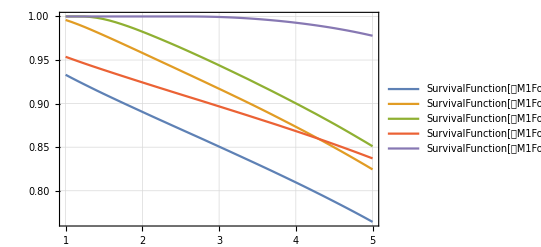

```mathematica
Plot[{
    SurvivalFunction[𝒟M1FormationEmp[0.4], x], 
    SurvivalFunction[𝒟M1FormationEmp[0.4, zMax -> zMaxE], x], 
    SurvivalFunction[𝒟M1FormationEmp[0.4, tdmax -> tdmaxE], x],
    SurvivalFunction[𝒟M1FormationEmp[0.4, tdmin -> tdminE], x],
    SurvivalFunction[𝒟M1FormationEmp[0.4, k -> 0.5], x]
  }, {x, 1, 5}, MaxRecursion->0, PlotRange->All, PlotTheme->"Detailed"]
```

```mathematica
Echo[{probabilityMminApprox[2], findSigma[probabilityMminApprox[2]]}, "Probability and tension level in sigmas, current data: "];
Echo[{probabilityMminDoubleApprox[2], findSigma[probabilityMminDoubleApprox[2]]}, "Probability and tension level in sigmas, future data: "];
```

Probability and tension level in sigmas, current data:   {0.000234232,3.67891}

Probability and tension level in sigmas, future data:   {5.48648×10^-8,5.43478}

### Probabilities related with minimum mass from the above distributions

Hence, with m_th = 2, the standard CCBH with k =3 is explided at more than 3 σ. Note that the approximation is quite good.

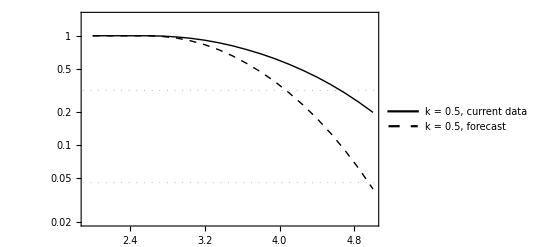

pathOut/plotProbabiliyNull005.pdf

```mathematica
frameTicksSmall = Flatten[Table[{n 10^i, "", tickSmall}, {n,1,10}, {i, -10, 0, 1}],1];
frameTicksLarge = Table[{10^i, Superscript[10, i], tickLarge}, {i, -10, 0, 1}];
frameTicks = Join[frameTicksSmall, frameTicksLarge];
tickLarge = 0.015;
tickSmall = 0.006;


plotProbabiliyNull005 = Block[
  {
    list = {#, probabilityMminApprox[#, k-> 0.5] } & /@ Range[2,5,0.15],
    list2 = {#, probabilityMminDoubleApprox[#, k-> 0.5] } & /@ Range[2,5,0.15]
  },
  ListLogPlot[{list, list2}, 
    Joined->True,
    PlotStyle->{{Thick, Black}, {Thick, Black, Dashed}},
    Background->White,
    Frame -> True,
    Axes -> False,
    FrameStyle-> Directive[Black, FontSize -> 13],
    FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
    FrameTicks->{{frameTicks, {{outSigma[1], "1σ"}, {outSigma[2], "2σ"}, {outSigma[3], "3σ"}}}, {Automatic, Automatic}},
    GridLines->{None, {outSigma[1], outSigma[2], outSigma[3]}},
    GridLinesStyle->Directive[Gray, Dotted],
    PlotLegends-> Placed[
      {Style["k = 0.5, current data", FontFamily->"Times", FontSize -> 14], Style["k = 0.5, forecast", FontFamily->"Times", FontSize -> 14]}, 
      {0.3,0.3}
    ],
    PlotRange->{All, {2 10^-2, 1.5}}
  ]
]

exportOut["plotProbabiliyNull005.pdf", plotProbabiliyNull005]
```

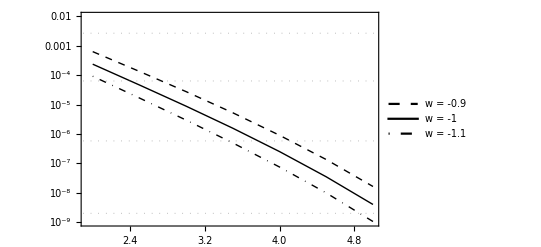

pathOut/plotProbabilityNullw.pdf

```mathematica
list1 = {#, probabilityMminApprox[#]} & /@ Range[2,5,0.5];
list2 = {#, probabilityMminApprox[#, k-> 3 0.9 , w-> -0.9]} & /@ Range[2,5,0.5];
list3 = {#, probabilityMminApprox[#, k-> 3 1.1 , w-> -1.1 ]} & /@ Range[2,5,0.5];

plotProbabilityNullw = ListLogPlot[{list2, list1, list3}, 
  Joined->True,
  PlotStyle->{{Thick, Dashed, Black}, {Thick, Black}, {Thick, DotDashed, Black}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  FrameTicks->{{frameTicks, {{outSigma[1], "1σ"}, {outSigma[2], "2σ"}, {outSigma[3], "3σ"}, {outSigma[4], "4σ"}, {outSigma[5], "5σ"}, {outSigma[6], "6σ"}}}, {Automatic, Automatic}},
  PlotRange->{All, {10^-9,  10^-2}},
  GridLines->{None, {outSigma[1], outSigma[2], outSigma[3], outSigma[4], outSigma[5], outSigma[6]}},
  GridLinesStyle->Directive[Gray, Dotted],
  PlotLegends-> Placed[
    {
      Style["w = -0.9", FontFamily->"Times", FontSize -> 12], 
      Style["w = -1", FontFamily->"Times", FontSize -> 12], 
      Style["w = -1.1", FontFamily->"Times", FontSize -> 12]
    },
    {0.8,0.76}
  ]
]

exportOut["plotProbabilityNullw.pdf", plotProbabilityNullw]
```

## Plots for the illustration with arrows

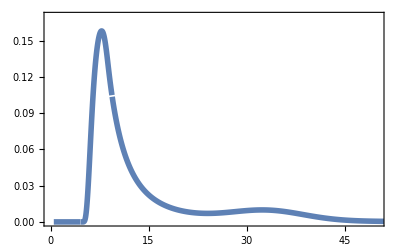

plotArrowsMerger.pdf

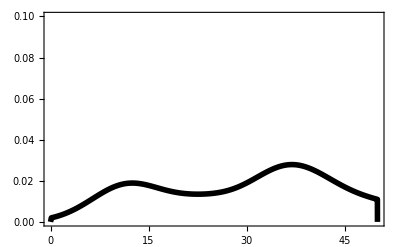

plotArrowsObs.pdf

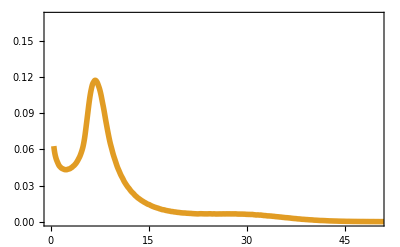

plotArrowsCCBH.pdf

```mathematica
plotArrowsMerger = Plot[
  {PDF[𝒟plp, x]}, 
  {x,0.5,100}, 
  PlotRange-> {{0,50}, {0,0.17}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotPoints->2700,
  MaxRecursion->0,
  PlotStyle->{{Thickness[0.01], ColorData[97, "ColorList"][[1]]}}
]

Export["plotArrowsMerger.pdf", plotArrowsMerger]

plotArrowsObs = SmoothHistogram[
  mXzDataForPlotting[[All,2]] /. Around[x_,y_] ->  x, 
  5, 
  "PDF",  
  PlotRange->{{0,50}, {0,.10}}, 
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotStyle->{{Thickness[0.01], Black}}
]

Export["plotArrowsObs.pdf", plotArrowsObs]

plotArrowsCCBH = Plot[
  {PDF[𝒟m1Formation, x]}, 
  {x,0.5,100}, 
  PlotRange-> {{0,50}, {0,0.17}},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"],
  PlotPoints->2700,
  MaxRecursion->0,
  PlotStyle->{{Thickness[0.01], ColorData[97, "ColorList"][[2]]}}
]

Export["plotArrowsCCBH.pdf", plotArrowsCCBH]
```

```mathematica
Plot[PDF[𝒟M1Formation[0.4], x], {x, 0,100}]
```

DataDistribution[<<SmoothKernel>>, {199307}]

## Formation mass distribution straight from observational data

```mathematica
Clear[dataM1ObsFormation];
mXzDataCentralValues = mXzDataForPlotting /. Around[x_, y_] -> x;

dataM1ObsFormation[k_, w_] := dataM1ObsFormation[k, w] =  #2 RandomVariate[𝒟InvMassFactor[#1, k, w], 10^5] &  @@@ mXzDataCentralValues;
```

```mathematica
dataM1ObsFormation[k0, w0] // EchoTiming; (*Check if it indeed has to be so long this computation*)
```

156.571

```mathematica
dataM1ObsFormationk0w0 = dataM1ObsFormation[k0, w0];
DumpSave["dataM1ObsFormationk0w0.mx", dataM1ObsFormationk0w0];
```

```mathematica
dataM1ObsFormation[k0, w0] // EchoTiming;

histFormationDistTest = Histogram[
  dataM1ObsFormation[k0, w0], 
  {0.4}, 
  "PDF", 
  PlotRange->{{0,100}, All},
  Background->White,
  Frame -> True,
  Axes -> False,
  FrameStyle-> Directive[Black, FontSize -> 13],
  FrameTicksStyle-> Directive[Black, FontFamily-> "Times"]
]
```

3.×10^-6

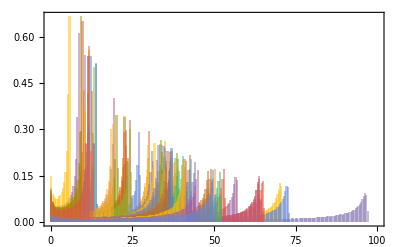

```mathematica
Clear[𝒟M1ObsFormation];
𝒟M1ObsFormation[bhNumber_, k_, w_] := 𝒟M1ObsFormation[bhNumber, k, w] = SmoothKernelDistribution[
  dataM1ObsFormation[k, w][[bhNumber]],
  0.1, 
  InterpolationPoints -> 10^5, 
  MaxExtraBandwidths -> {0,0}, 
  PerformanceGoal->"Quality"
]
```

```mathematica
𝒟M1ObsFormation[#, k0, w0] & /@ Range[72] // EchoTiming;
```

24.3162

```mathematica
PDF[𝒟M1ObsFormation[1, k0, w0], 20]
```

0.0142567

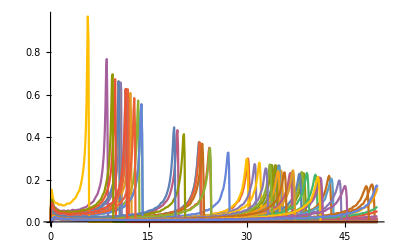

```mathematica
Block[
  {list = Table[{#, PDF[𝒟M1ObsFormation[i, k0, w0], #]} & /@ Range[0, 50, 0.1], {i,72}]},
  ListPlot[list, Joined->True, PlotRange->All]
]
```

```mathematica
probabilityGoodMass[bhNumber_, minimumMass_] := NProbability[m1 > minimumMass, m1 \[Distributed] 𝒟M1ObsFormation[bhNumber, k0, w0]];

totalProbabilityGoodMass[minimumMass_] := Product[probabilityGoodMass[bhNumber, minimumMass], {bhNumber, 1, 72}];
```

```mathematica
totalProbabilityGoodMass[2]
```

0.0101338

```mathematica
FindRoot[NProbability[Abs[x] > x0, x\[Distributed]NormalDistribution[]]==0.01 , {x0 , 2}]
```

{x0→2.57583}